```mathematica
c = 3 * 10^8;
G = 6.67 * 10^(-11);
SolarMass = 1.989* 10^30;
AU = 1.4955*10^11;
radius = 5 * AU;
timeOfAction = 86400;
desiredPrecision = 5;
repitionsPerGraph= 5;
totalCyclesToRun = 200;

InitializeBlackHoleArray := Module[{},
	numBlackHoles = Input["How many black holes are there in the system?"];
	PopulateInitialXVelocities[];
	PopulateInitialYVelocities[];
	PopulateInitialMasses[];
	blackHoleArray = Array[{radius * Cos[2π /numBlackHoles *  #], radius * Sin[2π / numBlackHoles *  #], initialXVelocities[[#]], initialYVelocities[[#]], masses[[#]]}&,numBlackHoles];
	blackHoleArrayTemp = blackHoleArray;
]

InitializeBlackHoleArrayCustom[xPositions_, yPositions_, xVels_, yVels_, masses_] := Module[{},
	blackHoleArray = Array[{xPositions[[#]] * radius, yPositions[[#]] * radius, xVels[[#]], yVels[[#]], (masses[[#]] * SolarMass)}&,Length[xPositions]];
	blackHoleArrayTemp = blackHoleArray;
]

XPos[objectNumber_Integer] := Module[{xposition},
	xposition = blackHoleArray[[objectNumber]][[1]]
]

YPos[objectNumber_Integer] := Module[{yposition},
	yposition = blackHoleArray[[objectNumber]][[2]]
]

XVel[objectNumber_Integer] := Module[{xVelocity},
	xVelocity= blackHoleArray[[objectNumber]][[3]]
]

YVel[objectNumber_Integer] := Module[{yVelocity},
	yVelocity= blackHoleArray[[objectNumber]][[4]]
]

Mass[objectNumber_Integer] := Module[{mass},
	mass = blackHoleArray[[objectNumber]][[5]]
]

SetXPos[objectNumber_Integer, newPosition_] := Module[{},
	blackHoleArrayTemp[[objectNumber]][[1]] = newPosition;
]

SetYPos[objectNumber_Integer, newPosition_] := Module[{},
	blackHoleArrayTemp[[objectNumber]][[2]] = newPosition;
]

SetXVel[objectNumber_Integer, newVelocity_] := Module[{},
	blackHoleArrayTemp[[objectNumber]][[3]] = newVelocity;
]

SetYVel[objectNumber_Integer, newVelocity_] := Module[{},
	blackHoleArrayTemp[[objectNumber]][[4]] = newVelocity;
]

DistanceToObject[currentObject_Integer, distantObject_Integer] := Module[{distance, x1, x2, y1, y2},
	x1 = blackHoleArray[[currentObject]][[1]];
	x2 = blackHoleArray[[distantObject]][[1]];
	y1 = blackHoleArray[[currentObject]][[2]];
	y2 = blackHoleArray[[distantObject]][[2]];
	distance = Sqrt[(x2 -x1)^2 + (y2 - y1)^2]
]

(* Get initial x velocities of black holes *)
PopulateInitialXVelocities[] := Module[{i = 1},
	While[i ≤ numBlackHoles, 
		AppendTo[initialXVelocities, Input[StringForm["What is the initial x velocity of black hole ``?", i]]]; 
		i++
	];
]

(* Get initial y velocities of black holes *)
PopulateInitialYVelocities[] := Module[{i = 1},
	While[i ≤ numBlackHoles, 
		AppendTo[initialYVelocities, Input[StringForm["What is the initial y velocity of black hole ``?", i]]]; 
		i++
	];
]

(* Get initial masses of black holes *)
PopulateInitialMasses[] := Module[{i = 1},
	While[i ≤ numBlackHoles, 
		AppendTo[masses, Input[StringForm["What is the initial mass of black hole ``?", i]] * SolarMass]; 
		i++
	];
]

VectorQuadrant[vector_] := Module[{quadrantNumber},
	If[Positive[ vector[[1]] ], If[Positive[ vector[[2]] ], quadrantNumber = 1, quadrantNumber = 4], If[Positive[ vector[[2]] ], quadrantNumber = 2, quadrantNumber = 3] ];
	quadrantNumber
]

ComponentForce[currentObject_Integer, distantObject_Integer, xory_Integer] := Module[{component}, 
	v1 =  {XPos[distantObject] - XPos[currentObject], YPos[distantObject] - YPos[currentObject]};
	v2 = {1,0};
	angle = VectorAngle[v1, v2];
	quadrant = VectorQuadrant[v1];
	If[(quadrant == 3 || quadrant == 4), angle = 2π - angle];
	If[xory == 2, component = Sin[angle], component = Cos[angle]];
	component
]

SumForces[objectNumber_Integer, xory_Integer] := Module[{totalForce}, 
	n = 1;
	totalForce = 0;
	While[n < objectNumber,
		totalForce += G * Mass[objectNumber]  * Mass[n] / ((DistanceToObject[objectNumber, n])^2) * ComponentForce[objectNumber, n, xory];
		++n
	];
	n += 1;
	While[n < (Length[blackHoleArray] + 1), 
		totalForce += G * Mass[objectNumber]  * Mass[n] / ((DistanceToObject[objectNumber, n])^2) *  ComponentForce[objectNumber, n, xory]; 
		++n
	];
	totalForce
]

NewData[objectNumber_Integer] := Module[{},
	xForce = SumForces[objectNumber, 1];
	newXVel = N[(xForce * timeOfAction / Mass[objectNumber]), desiredPrecision];
	relativeXVel = (newXVel + XVel[objectNumber]) / (1 + (newXVel * XVel[objectNumber] / c^2)); 
	SetXVel[objectNumber, N[relativeXVel, desiredPrecision]];
	newXPos = XPos[objectNumber] + relativeXVel * timeOfAction;
	SetXPos[objectNumber, N[newXPos, desiredPrecision]];

	yForce = SumForces[objectNumber, 2];
	newYVel =  N[(yForce * timeOfAction / Mass[objectNumber]), desiredPrecision];
	relativeYVel = (newYVel + YVel[objectNumber]) / (1 + (newYVel * YVel[objectNumber] / c^2)); 
	SetYVel[objectNumber, N[relativeYVel, desiredPrecision]];
	newYPos = YPos[objectNumber] + relativeYVel * timeOfAction;
	SetYPos[objectNumber, N[newYPos, desiredPrecision]];
]

GraphAndShowMotion := Module [{},
	n=1;
	xGraph={};
	yGraph={};
	xVGraph={};
	yVGraph={};
	graph={};
	While[n ≤ Length[blackHoleArray],
		AppendTo[xGraph, XPos[n]];
		AppendTo[yGraph, YPos[n]]; 
		++n
	];
	n = 1;
	While[n ≤ Length[blackHoleArray],
		AppendTo[xVGraph, (XVel[n] * timeOfAction +XPos[n])];
		AppendTo[yVGraph, (YVel[n] * timeOfAction +YPos[n])]; 
		++n
	];
	n = 1;
	While[n ≤ Length[blackHoleArray],
		AppendTo[graph, {{xGraph[[n]], yGraph[[n]]} , {xVGraph[[n]], yVGraph[[n]]}}];
		++n
	];
	Graphics[
		{Blue, Arrowheads[Medium], Arrow[#]}& /@ graph, Axes->True, AspectRatio->1, Background->White, PlotRange->{{-2 * radius, 2 * radius}, {-2 * radius, 2 * radius}}
	]
]

(*GraphAndShowPotentials := Module [{};





]*)

RunCycles := Module[{},
	cyclesRun = 0;
	Print[GraphAndShowMotion];
	While[cyclesRun < totalCyclesToRun,
		repitionCounter = 0;
		While [repitionCounter < repitionsPerGraph,
			num = 1;
			While[num  ≤  Length[blackHoleArray],
				NewData[num];
				++num;
			];
			blackHoleArray = blackHoleArrayTemp;
			++repitionCounter;
		];
		AppendTo[AnimationList, GraphAndShowMotion];
		++cyclesRun;
	];
]
```

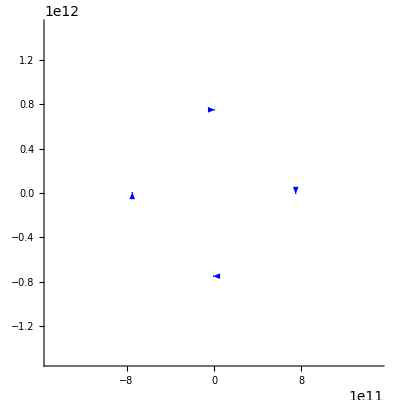

```mathematica
(*blackHoleArray = {};
blackHoleArrayTemp = {};
initialXVelocities = {};
initialYVelocities = {};
masses = {};
AnimationList = {};
InitializeBlackHoleArray;
RunCycles;
ListAnimate[AnimationList, 10]*)
```

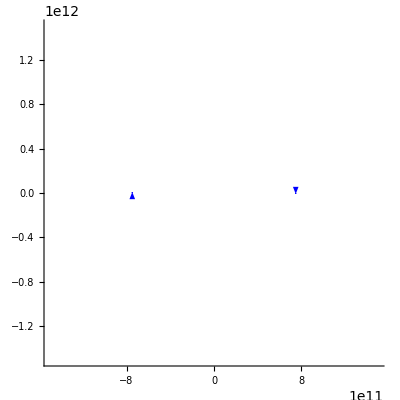

```mathematica
blackHoleArray = {};
blackHoleArrayTemp = {};
IXP = {1, -1};
IYP  = {0, 0};
IXV = {0, 0};
IYV = {-100000, 100000};
M= {500, 500};
InitializeBlackHoleArrayCustom[IXP, IYP, IXV, IYV, M];
AnimationList = {};
RunCycles;
ListAnimate[AnimationList, 10]
```

```mathematica
(*blackHoleArray = {};
blackHoleArrayTemp = {};
IXP = {1, -1, 0};
IYP  = {0, 0, -2};
IXV = {0, 0, 0};
IYV = {-100000, 100000, 0};
M= {500, 500, .01};
InitializeBlackHoleArrayCustom[IXP, IYP, IXV, IYV, M];
AnimationList = {};
RunCycles;
ListAnimate[AnimationList, 1]*)
```

-Graphics-